# Pruebas con el ensamble de Ginibre

Un estado bipartito puede ser expresado como combinación lineal de la base computacional (dimensión 4). En general, tendrá cuatro coeficientes complejos que pueden organizarse en una matriz de 2 x 2. Como nosotros generamos esos coeficientes complejos muestreándolos de la distribución normal, la matriz de 2 x 2 coincide con una matriz del ensamble de Ginibre. Sin embargo, la normalización de los estados no me termina de encajar en estos razonamientos. A continuación se harán pruebas para dilucidar este problema.

```mathematica
Needs["CoolTools`"]
Needs["Quantum`"]
```

En el artículo de ‘Entanglement Typicality’ se menciona que para generar estados puros distribuidos con la medida de Haar se fija un estado y se le aplican unitarias aleatorias Haar. Se dice también que este proceso es equivalente a generar sólo las matrices unitarias Haar y tomarles una de sus columnas. (No sé por qué lo anterior es válido, pero sería genial).
Para generar las unitarias Haar se puede hacer lo siguiente: Generar matrices del ensamble de Ginibre, aplicar Gram-Schmidt a sus columnas para obtener una matriz unitaria y tomar la primera de estas columnas. En el artículo de Mezzadri se afirma que generar matrices unitarias con Gram-Schmidt sobre el ensamble de Ginibre las genera distribuidas con la medida de Haar, sin embargo este proceso es numéricamente inestable. No se indica con qué valores de promedio y varianza se deben generar las entradas de las matrices de Ginibre, por lo que al generarlas con media cero creo que saldrán kets puros. Por ahora no importa si el proceso es estable o no, pues no queremos generar las matrices completas sino sólo obtener sus primeras columnas, las cuales se generarán tan sólo normalizando el primer vector de las matrices de Ginibre.

## Generando matrices del ensemble de Ginibre y generando kets puros

Las matrices del ensemble de Ginibre sólo son matrices cuyas entradas son variables aleatorias complejas normales estándar i. i. d. Al ser independientes asumiré que su matriz de correlación es la matriz identidad. Sus entradas tendrán media igual a cero.

NOTA: Muchos artículos indican que las entradas de las matrices deben tener distribución N(0,1/2) para que la función de densidad de las variables aleatorias en cuestión tenga a la identidad como matriz de correlación. No entiendo la razón detrás de esto, puesto que además, nosotros generamos las variables aleatorias con distribución N(0,1). Dejaremos esta varianza como un parámetro para ver qué sucede en cada caso.

```mathematica
(*Función general que devuelve una lista de matrices de Ginibre de dimensión N x M, con media μ y varianza σ*)
ginibreEnsembleList[samplesize_, N_, M_, μ_, σ_]:= Table[Table[Complex @@ RandomVariate[NormalDistribution[μ,σ], 2],{i,N},{j,M}], samplesize]
```

```mathematica
(*Prueba de uso*)
MatrixForm /@ ginibreEnsembleList[3, 2, 2, 0, 1]
```

{(-0.02896+1.10075 ⅈ | -0.115487+0.355237 ⅈ
1.99904+1.04926 ⅈ | 0.741836+0.165423 ⅈ),(-0.304083-1.89697 ⅈ | 2.06146-0.149457 ⅈ
0.799934-1.06224 ⅈ | -1.82369+0.127617 ⅈ),(0.0294716-1.75258 ⅈ | 0.178568+1.32704 ⅈ
1.78907-0.876833 ⅈ | 0.622764-0.900642 ⅈ)}

Ahora, se supone que tomando la media 0 y la varianza finita se recuperan los estados puros

```mathematica
dim = 1;
media = 0;
varianza = 1/2;
```

```mathematica
edospurosGinibre = Flatten /@ ginibreEnsembleList[1000, 2, dim, media, varianza];
```

```mathematica
Mean[Norm /@ edospurosGinibre]
```

0.935116

Veamos qué pasa si revisamos distintos valores para la varianza:

```mathematica
varianzas = Table[0.1 i, {i,20}]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.}

```mathematica
multipleVariancesGinibreKets = Map[(Flatten /@ ginibreEnsembleList[100, 2, dim, media, #])&, varianzas];
```

```mathematica
Map[(Mean[Norm /@ #])&, multipleVariancesGinibreKets]
```

{0.191711,0.382197,0.557474,0.774654,0.915905,1.03323,1.22968,1.60968,1.65866,1.79002,2.05711,2.285,2.45826,2.49893,2.78862,2.93245,3.14422,3.42782,3.6766,3.92673}

Curiosamente, con varianza igual a 0.5 el respectivo conjunto de kets tiene la norma más cercana a 1. Veamos qué pasa con una varianza entre 0.5 y 0.6:

```mathematica
edosPurosGinibreSpecificVar = Flatten /@ ginibreEnsembleList[1000, 2, dim, media, 0.528];
```

```mathematica
Mean[Norm /@ edosPurosGinibreSpecificVar]
```

0.969183

Bueno, pues parece que sólo generando matrices de Ginibre no salen normalizados los vectores con seguridad. De hecho no tendría por qué ser así, pero en el artículo de Entanglement Typicality se entiende algo así. Para varianzas entre 0.5 y 0.6 puede acercarse, pero nos gustaría ser exactos. Por otro lado, en el mismo artículo, se menciona que tomar la primera columna de unitarias Haar (generadas a partir del ensemble de Ginibre con Gram-Schimdt) ya nos da kets puros distribuidos con la medida de Haar. Así, sólo basta con normalizar las primeras columnas de la muestra de matrices que acabamos de generar.

## Generando kets puros con unitarias Haar, con nuestro método y con el ensemble GUE

Compararemos a continuación estas tres formas de generar estados.

### Unitarias Haar a partir del ensemble de Ginibre

```mathematica
(*Generamos muchas matrices del ensemble de Ginibre. Para generar edos de un qubit, necesitaremos matrices de 2 x 2. Tomaremos después sólo la primera columna
de cada una de ellas*)
matricesGinibre = ginibreEnsembleList[10000, 2, 2, 0, 1];
```

```mathematica
(*Ahora, convertimos las matrices en unitarias Haar al aplicarles Gram-Schmidt a sus columnas*)
unitariasHaar = Map[Transpose[Orthogonalize[Transpose[#], Method->"GramSchmidt"]]&, matricesGinibre];
```

```mathematica
(*Aplicamos las unitarias a un ket fijo. En este caso al ket {1,0}*)
ketsHaar = Map[#.{1,0} &, unitariasHaar];
BVsHaar = densityMatrixToPoint[ketsToDensity[ketsHaar], NQubitBasis[1]];
```

```mathematica
(*Distribución de los puntos en la esfera de Bloch*)
sphBVsAzimuthalHaar = ToSphericalCoordinates[#][[3]]& /@ BVsHaar;
distPlotHaar = Histogram[sphBVsAzimuthalHaar, Automatic, "Probability", PlotRange->{{-Pi+0.1, Pi-0.1}, Automatic}];
```

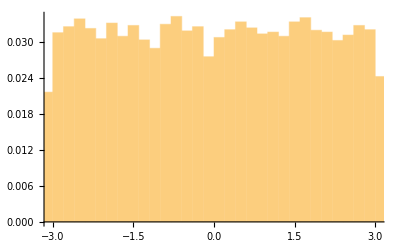
-Graphics3D- | -Graphics-

```mathematica
Grid[{{Show[SphericalPlot3D[1, θ, ϕ, PlotStyle->Opacity[0.1]], ListPointPlot3D[BVsHaar]], distPlotHaar}
}]
```

### Nuestro método

```mathematica
ketsOurs = randomKets[2, 10000];
BVsOurs = densityMatrixToPoint[ketsToDensity[ketsOurs], NQubitBasis[1]];
```

```mathematica
sphBVsAzimuthalOurs = ToSphericalCoordinates[#][[3]]& /@ BVsOurs;
distPlotOurs = Histogram[sphBVsAzimuthalOurs, Automatic, "Probability"];
```

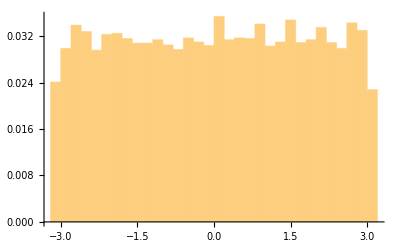
-Graphics3D- | -Graphics-

```mathematica
Grid[{{Show[SphericalPlot3D[1, θ, ϕ, PlotStyle->Opacity[0.1]], ListPointPlot3D[BVsOurs]], distPlotOurs}
}]
```

### Con el ensemble GUE

```mathematica
unitariasGUE = MatrixExp[-I 0.01 #]& /@ RandomVariate[GaussianUnitaryMatrixDistribution[2], 100000];
```

```mathematica
ketsGUE = #.{1, 0}& /@ unitariasGUE;
BVsGUE = densityMatrixToPoint[ketsToDensity[ketsGUE], NQubitBasis[1]];
```

```mathematica
cylBVsAngleGUE = #[[2]]& /@ toCylindricalCoordinates[BVsGUE];
distPlotGUE = Histogram[cylBVsAngleGUE, Automatic, "Probability"];
```

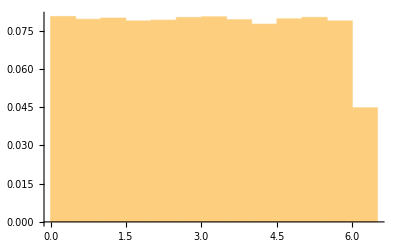
-Graphics3D- | -Graphics-

```mathematica
Grid[{{Show[SphericalPlot3D[1, θ, ϕ, PlotStyle->Opacity[0.1]], ListPointPlot3D[BVsGUE]], distPlotGUE}
}]
```

```mathematica
Min[(#[[3]]& /@ BVsGUE)]
```

0.997327